```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/corradini/FF

```mathematica
Changerules=Import["myintegrals.sol.m"]/.{INT[a_,_,_,_,_,{b__}]:>ToExpression[a][b]};
MastersF5=Import["MIF5.m"];
MastersF6=Import["MIF6.m"];
MastersF1=Import["MIF1.m"];
MastersF2=Import["MIF2.m"];
MastersF3=Import["MIF3.m"];
MastersF4=Import["MIF4.m"];
MastersF8=Import["MIF8.m"];
MastersF9=Import["MIF9.m"];
ResF5=Import["F5result.m"];
ResF6=Import["F6result.m"];
ResF1=Import["F1result.m"];
ResF2=Import["F2result.m"];
ResF3=Import["F3result.m"];
ResF4=Import["F4result.m"];
ResF8=Import["F8result.m"];
ResF9=Import["F9result.m"];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../fire/FIRE6"]
```

/Users/corradini/fire/FIRE6

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Thu 20 Nov 2025 13:50:10
Read from:/Users/corradini/LiteRed2/Source/LiteRed2025.m (CRC32:749265139,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Declare[{k1,k2,k3,p1,p2},Vector,{r},Number];
```

```mathematica
sp[p1,p1]=0;sp[p2,p2]=0;sp[p1,p2]=r/2;
```

#### F5

```mathematica
NewDsBasis[F5,{k1·k1,k2·k2,k3·k3,(-k1+p1)·(-k1+p1),(k2+p2)·(k2+p2),(-k1-k2+p1)·(-k1-k2+p1),(k2+k3+p2)·(k2+k3+p2),(-k1-k2-k3+p1)·(-k1-k2-k3+p1),(k1+k2+k3+p2)·(k1+k2+k3+p2),(k2+k3)·(k2+k3),(k1+k3+p2)·(k1+k3+p2),(k3+p1)·(k3+p1)},{k1,k2,k3},Directory->"F5dir"]
```

F5 is valid basis. The definitions of the basis will be saved in "F5dir" directory.
    Ds[F5] — denominators,
    SPs[F5] — scalar products involving loop momenta,
    LMs[F5] — loop momenta,
    EMs[F5] — external momenta,
    Parameters[F5] — parameters (invariants, masses, dimension),
    Toj[F5] — rules to transform scalar products to denominators,
    CutDs[F5] — flag vector of cut denominators.

F5

```mathematica
topo5={{1->2,0},{3->4,0},{5->6,0},{1->3,0},{4->6,0},{3->5,0},{6->2,0},{5->7,0},{2->7,0},{-1->1,p1},{-4->4,p2},{-7->7, p3}}
```

{{1→2,0},{3→4,0},{5→6,0},{1→3,0},{4→6,0},{3→5,0},{6→2,0},{5→7,0},{2→7,0},{-1→1,p1},{-4→4,p2},{-7→7,p3}}

```mathematica
SetOptions[FeynGraphPlot,EdgeLabels->True,Frame->False]
```

{GraphLayout→SpringElectricalEmbedding,VertexCoordinates→Automatic,EdgeLabels→True,EdgeStyle→{_→{GrayLevel[0]}},VertexStyle→{_→{GrayLevel[0],Disk[{0,0}]}},VertexSize→{_→0.003},VertexLabels→None,VertexLabelStyle→{RGBColor[1, 0, 0]},Background→None,Frame→False,FrameLabel→None,FrameStyle→{},LabelStyle→{},ImageMargins→0,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→RGBColor[1, 0, 0],MultiedgeStyle→Automatic,PackingMethod→Automatic,PlotLabel→None,Epilog→{}}

```mathematica
AttachGraph[js[F5,1,1,1,1,1,1,1,1,1,0,0,0],topo5]
```

```mathematica
todrawF5=MastersF5/.{1,{a__}}:>j[F5,a]
```

{j[F5,0,0,0,0,1,1,1,0,1,0,0,0],j[F5,0,0,1,1,0,1,1,0,1,0,0,0],j[F5,0,0,1,1,1,0,0,1,1,0,0,0],j[F5,0,0,1,1,1,1,1,0,1,0,0,0],j[F5,0,1,1,1,1,1,1,1,1,0,0,0],j[F5,1,0,0,0,1,1,0,1,1,0,0,0],j[F5,1,0,0,0,1,1,1,1,0,0,0,0],j[F5,1,0,1,1,1,1,0,1,1,0,0,0],j[F5,1,1,1,0,0,1,1,1,1,0,0,0],j[F5,1,1,1,1,0,0,1,1,1,0,0,0],j[F5,1,1,1,1,1,0,0,1,1,0,0,0],j[F5,1,1,1,1,1,1,0,0,1,0,0,0],j[F5,1,1,1,1,1,1,1,1,1,0,0,0]}

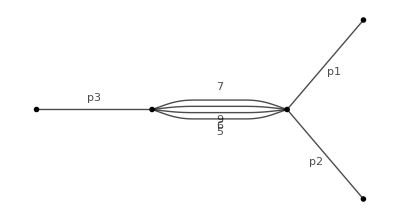
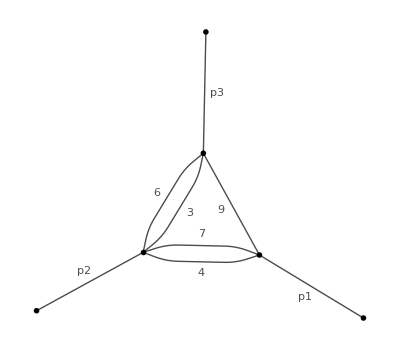
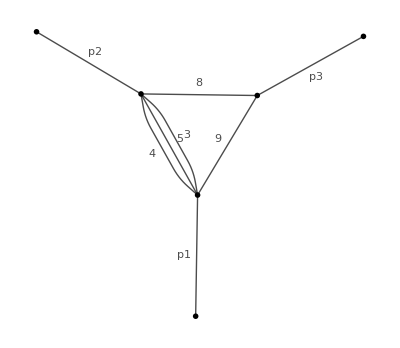
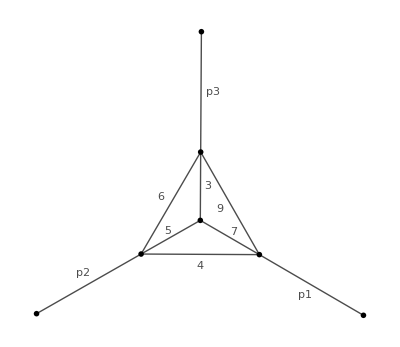
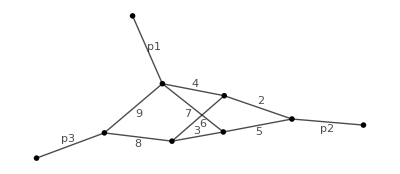
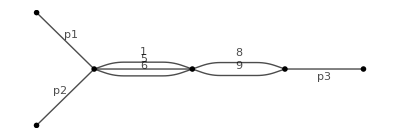
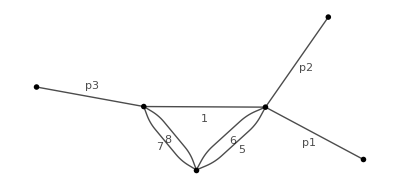
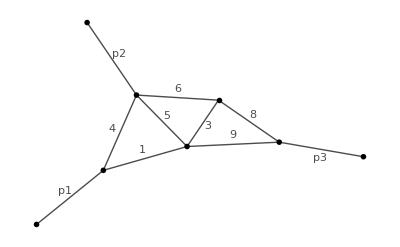

```mathematica
jGraphPlot/@todrawF5
```

#### F1

```mathematica
NewDsBasis[F1,{k1·k1,k2·k2,k3·k3,(-k1+p1)·(-k1+p1),(k1+p2)·(k1+p2),(-k1-k2+p1)·(-k1-k2+p1),(k1+k2+p2)·(k1+k2+p2),(-k1-k2-k3+p1)·(-k1-k2-k3+p1),(k1+k2+k3+p2)·(k1+k2+k3+p2),(k2+p2)·(k2+p2),(k2+k3+p2)·(k2+k3+p2),(k2+k3)·(k2+k3)},{k1,k2,k3},Directory->"F1dir"]
```

F1 is valid basis. The definitions of the basis will be saved in "F1dir" directory.
    Ds[F1] — denominators,
    SPs[F1] — scalar products involving loop momenta,
    LMs[F1] — loop momenta,
    EMs[F1] — external momenta,
    Parameters[F1] — parameters (invariants, masses, dimension),
    Toj[F1] — rules to transform scalar products to denominators,
    CutDs[F1] — flag vector of cut denominators.

F1

```mathematica
topo1={{1->2,0},{3->4,0},{5->6,0},{1->3,0},{2->4,0},{3->5,0},{4->6,0},{5->7,0},{6->7,0},{-1->1,p1},{-2->2,p2},{-7->7, p3}}
```

{{1→2,0},{3→4,0},{5→6,0},{1→3,0},{2→4,0},{3→5,0},{4→6,0},{5→7,0},{6→7,0},{-1→1,p1},{-2→2,p2},{-7→7,p3}}

```mathematica
AttachGraph[js[F1,1,1,1,1,1,1,1,1,1,0,0,0],topo1]
```

```mathematica
todrawF1=MastersF1/.{1,{a__}}:>j[F1,a]
```

{j[F1,0,0,0,1,1,1,1,1,1,0,0,0],j[F1,0,0,1,1,1,0,1,1,0,0,0,0],j[F1,0,1,1,0,1,0,0,1,0,0,0,0],j[F1,0,1,1,0,1,1,0,0,1,0,0,0],j[F1,0,1,1,1,1,0,0,1,1,0,0,0],j[F1,1,1,0,0,0,1,1,1,1,0,0,0],j[F1,1,1,1,0,0,0,0,1,1,0,0,0],j[F1,1,1,1,0,0,0,1,1,0,0,0,0],j[F1,1,1,1,0,1,1,0,1,1,0,0,0]}

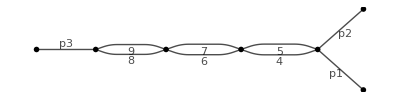
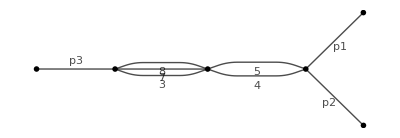
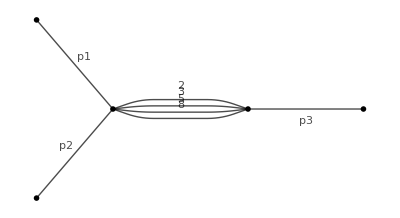
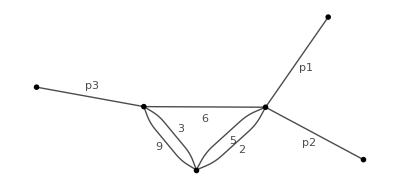
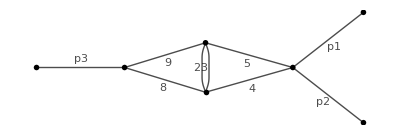
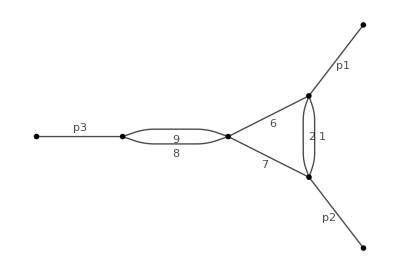
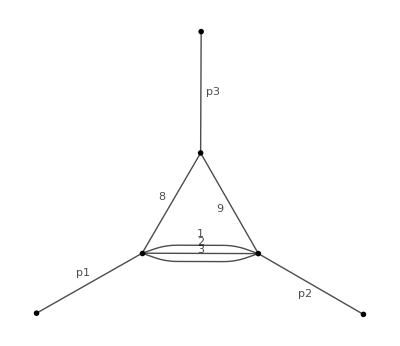
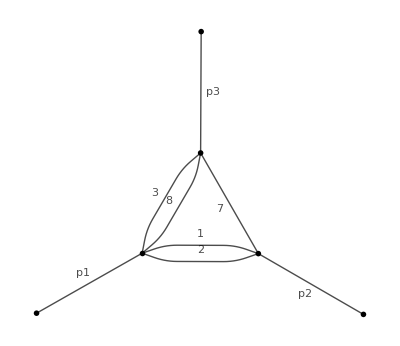

```mathematica
jGraphPlot/@todrawF1
```

#### F2

```mathematica
NewDsBasis[F2,{k1·k1,k2·k2,k3·k3,(-k1+p1)·(-k1+p1),(-k1-k2+p1)·(-k1-k2+p1),(k1+k2+p2)·(k1+k2+p2),(k1-k3+p2)·(k1-k3+p2),(k1-k3)·(k1-k3),(k2+k3)·(k2+k3),(k1+k2)·(k1+k2),(-k1-k2-k3+p1)·(-k1-k2-k3+p1),(k3+p2)·(k3+p2)},{k1,k2,k3},Directory->"F2dir"]
```

F2 is valid basis. The definitions of the basis will be saved in "F2dir" directory.
    Ds[F2] — denominators,
    SPs[F2] — scalar products involving loop momenta,
    LMs[F2] — loop momenta,
    EMs[F2] — external momenta,
    Parameters[F2] — parameters (invariants, masses, dimension),
    Toj[F2] — rules to transform scalar products to denominators,
    CutDs[F2] — flag vector of cut denominators.

F2

```mathematica
topo2={{1->5,0},{3->6,0},{5->6,0},{1->3,0},{3->7,0},{4->7,0},{2->4,0},{5->2,0},{6->4,0},{-1->1,p1},{-2->2,p2},{-7->7, p3}}
```

{{1→5,0},{3→6,0},{5→6,0},{1→3,0},{3→7,0},{4→7,0},{2→4,0},{5→2,0},{6→4,0},{-1→1,p1},{-2→2,p2},{-7→7,p3}}

```mathematica
AttachGraph[js[F2,1,1,1,1,1,1,1,1,1,0,0,0],topo2]
```

```mathematica
todrawF2=MastersF2/.{1,{a__}}:>j[F2,a]
```

{j[F2,0,0,1,1,0,1,0,0,1,0,0,0],j[F2,0,0,1,1,1,0,1,0,1,0,0,0],j[F2,0,0,1,1,1,1,0,1,1,0,0,0],j[F2,0,0,1,1,1,1,1,0,0,0,0,0],j[F2,0,1,0,1,0,1,0,1,1,0,0,0],j[F2,0,1,1,0,1,1,0,1,0,0,0,0],j[F2,0,1,1,1,0,1,0,1,1,0,0,0],j[F2,0,1,1,1,1,1,1,1,0,0,0,0],j[F2,1,1,0,0,1,1,0,1,1,0,0,0],j[F2,1,1,1,1,1,1,1,1,1,0,0,0]}

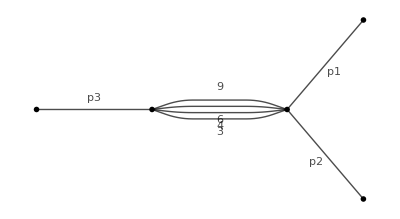
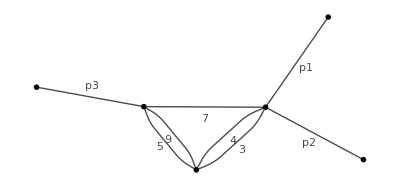
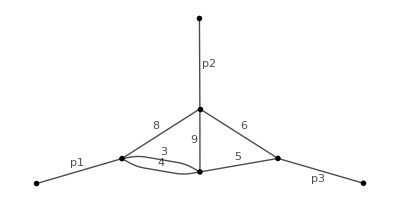
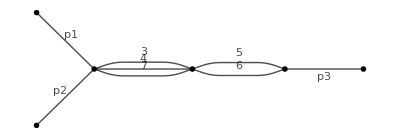
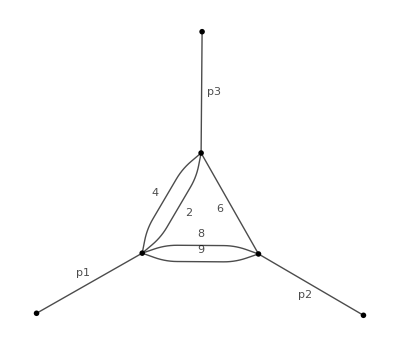
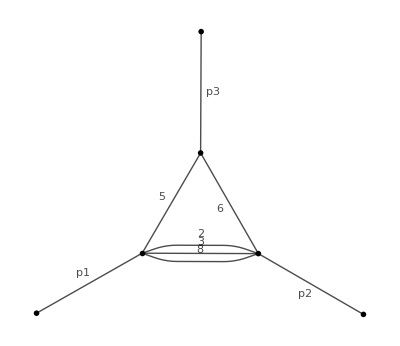
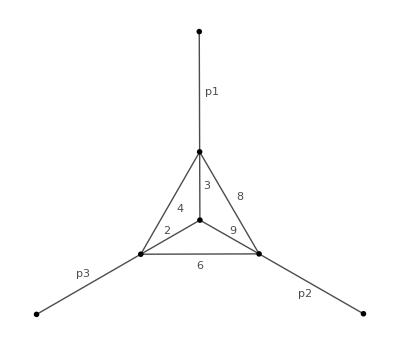
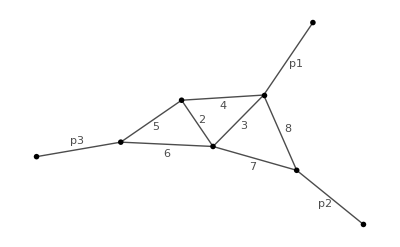

```mathematica
jGraphPlot/@todrawF2
```

#### F3

```mathematica
NewDsBasis[F3,{k1·k1,k2·k2,k3·k3,(-k1+p1)·(-k1+p1),(k1+p2)·(k1+p2),(-k1-k2+p1)·(-k1-k2+p1),(k1+k3+p2)·(k1+k3+p2),(-k1-k2-k3+p1)·(-k1-k2-k3+p1),(k1+k2+k3+p2)·(k1+k2+k3+p2),(k2+k3)·(k2+k3),(k1+k3)·(k1+k3),(k1+k2)·(k1+k2)},{k1,k2,k3},Directory->"F3dir"]
```

F3 is valid basis. The definitions of the basis will be saved in "F3dir" directory.
    Ds[F3] — denominators,
    SPs[F3] — scalar products involving loop momenta,
    LMs[F3] — loop momenta,
    EMs[F3] — external momenta,
    Parameters[F3] — parameters (invariants, masses, dimension),
    Toj[F3] — rules to transform scalar products to denominators,
    CutDs[F3] — flag vector of cut denominators.

F3

```mathematica
topo3={{1->2,0},{3->4,0},{5->6,0},{1->3,0},{2->6,0},{3->5,0},{4->6,0},{5->7,0},{4->7,0},{-1->1,p1},{-2->2,p2},{-7->7, p3}}
```

{{1→2,0},{3→4,0},{5→6,0},{1→3,0},{2→6,0},{3→5,0},{4→6,0},{5→7,0},{4→7,0},{-1→1,p1},{-2→2,p2},{-7→7,p3}}

```mathematica
AttachGraph[js[F3,1,1,1,1,1,1,1,1,1,0,0,0],topo3]
```

```mathematica
todrawF3=MastersF3/.{1,{a__}}:>j[F3,a]
```

{j[F3,0,0,0,0,1,1,1,0,1,0,0,0],j[F3,0,0,1,1,0,0,1,1,1,0,0,0],j[F3,0,0,1,1,0,1,1,0,1,0,0,0],j[F3,0,1,1,1,1,1,1,1,1,0,0,0],j[F3,1,0,0,0,0,1,1,1,1,0,0,0],j[F3,1,0,1,0,0,1,1,0,1,0,0,0],j[F3,1,1,1,0,0,1,1,0,1,0,0,0],j[F3,1,1,1,0,0,1,1,1,1,0,0,0]}

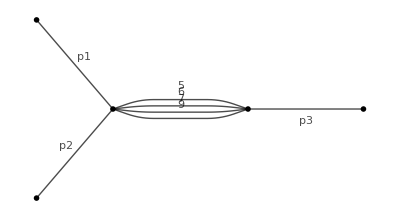
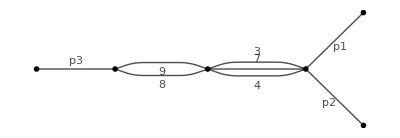
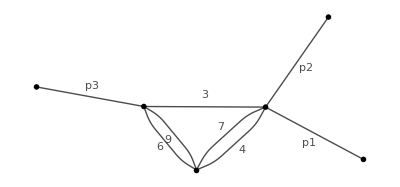
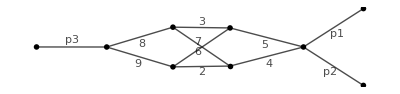
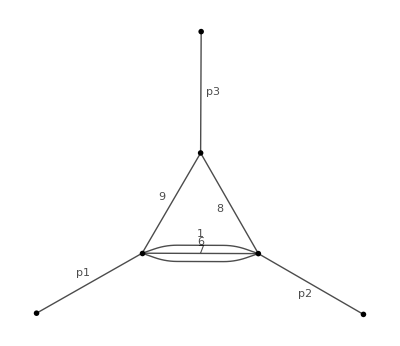
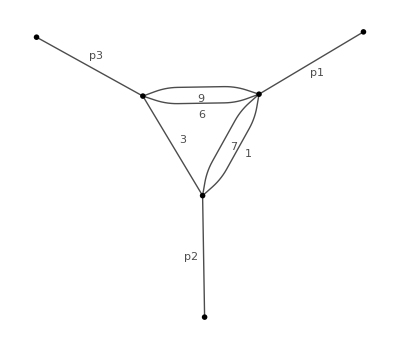
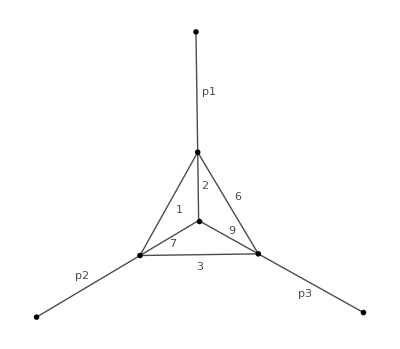
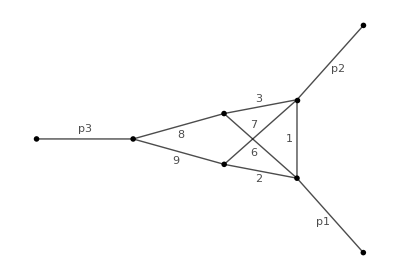

```mathematica
jGraphPlot/@todrawF3
```

#### F4

```mathematica
NewDsBasis[F4,{k1·k1,k2·k2,k3·k3,(-k1+p1)·(-k1+p1),(k2+p2)·(k2+p2),(-k1-k2+p1)·(-k1-k2+p1),(k1+k2+p2)·(k1+k2+p2),(-k1-k2-k3+p1)·(-k1-k2-k3+p1),(k1+k2+k3+p2)·(k1+k2+k3+p2),(k1+k2)·(k1+k2),(k2+k3)·(k2+k3),(k3+p2)·(k3+p2)},{k1,k2,k3},Directory->"F4dir"]
```

F4 is valid basis. The definitions of the basis will be saved in "F4dir" directory.
    Ds[F4] — denominators,
    SPs[F4] — scalar products involving loop momenta,
    LMs[F4] — loop momenta,
    EMs[F4] — external momenta,
    Parameters[F4] — parameters (invariants, masses, dimension),
    Toj[F4] — rules to transform scalar products to denominators,
    CutDs[F4] — flag vector of cut denominators.

F4

```mathematica
topo4={{1->2,0},{3->4,0},{5->6,0},{1->3,0},{4->2,0},{3->5,0},{2->6,0},{5->7,0},{6->7,0},{-1->1,p1},{-4->4,p2},{-7->7, p3}}
```

{{1→2,0},{3→4,0},{5→6,0},{1→3,0},{4→2,0},{3→5,0},{2→6,0},{5→7,0},{6→7,0},{-1→1,p1},{-4→4,p2},{-7→7,p3}}

```mathematica
AttachGraph[js[F4,1,1,1,1,1,1,1,1,1,0,0,0],topo4]
```

```mathematica
todrawF4=MastersF4/.{1,{a__}}:>j[F4,a]
```

{j[F4,0,0,1,1,1,0,0,1,1,0,0,0],j[F4,0,0,1,1,1,0,1,1,0,0,0,0],j[F4,0,1,1,1,0,0,0,0,1,0,0,0],j[F4,0,1,1,1,0,0,1,1,0,0,0,0],j[F4,1,1,0,1,1,1,1,1,1,0,0,0],j[F4,1,1,1,1,1,0,0,1,1,0,0,0],j[F4,1,1,1,1,1,0,1,1,0,0,0,0]}

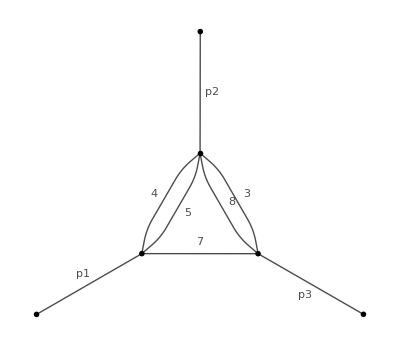
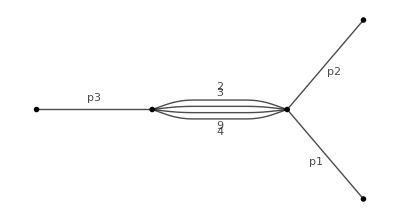
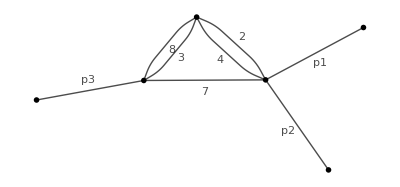
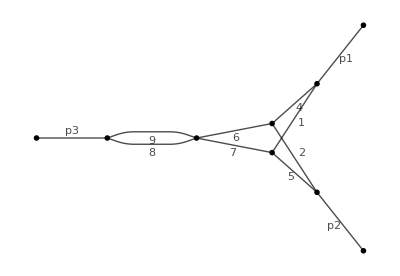
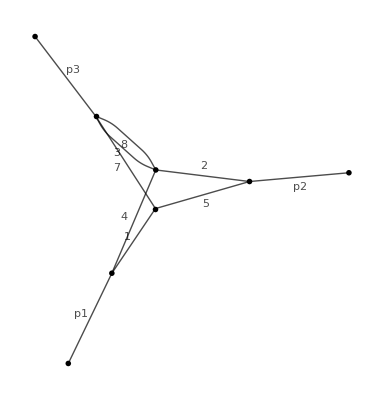
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
jGraphPlot/@todrawF4
```

#### F6

```mathematica
NewDsBasis[F6, {k1·k1,k2·k2,k3·k3,(-k1+p1)·(-k1+p1),(-k1-k2+p1)·(-k1-k2+p1),(-k1-k2-k3+p1)·(-k1-k2-k3+p1),(k1+k2+k3+p2)·(k1+k2+k3+p2),(k2+p2)·(k2+p2),(k2+k3+p2)·(k2+k3+p2),(-k1+p1+p2)·(-k1+p1+p2),(k1+k3)·(k1+k3),(k3+p1)·(k3+p1)},{k1,k2,k3},Directory->"F6dir"]
```

F6 is valid basis. The definitions of the basis will be saved in "F6dir" directory.
    Ds[F6] — denominators,
    SPs[F6] — scalar products involving loop momenta,
    LMs[F6] — loop momenta,
    EMs[F6] — external momenta,
    Parameters[F6] — parameters (invariants, masses, dimension),
    Toj[F6] — rules to transform scalar products to denominators,
    CutDs[F6] — flag vector of cut denominators.

F6

```mathematica
topo6={{1->2,0},{3->4,0},{5->6,0},{1->3,0},{3->5,0},{5->7,0},{2->7,0},{4->6,0},{6->2,0},{-1->1,p1},{-4->4,p2},{-7->7, p3}}
```

{{1→2,0},{3→4,0},{5→6,0},{1→3,0},{3→5,0},{5→7,0},{2→7,0},{4→6,0},{6→2,0},{-1→1,p1},{-4→4,p2},{-7→7,p3}}

```mathematica
AttachGraph[js[F6,1,1,1,1,1,1,1,1,1,0,0,0],topo6]
```

```mathematica
todrawF6=MastersF6/.{1,{a__}}:>j[F6,a]
```

{j[F6,0,0,0,0,1,0,1,1,1,0,0,0],j[F6,0,0,1,1,0,1,1,1,0,0,0,0],j[F6,0,0,1,1,1,0,1,0,1,0,0,0],j[F6,0,0,1,1,1,0,1,1,1,0,0,0],j[F6,0,1,1,1,1,1,1,1,1,0,0,0],j[F6,1,0,0,0,1,1,0,1,1,0,0,0],j[F6,1,0,0,0,1,1,1,1,0,0,0,0],j[F6,1,0,1,1,1,1,1,1,0,0,0,0],j[F6,1,1,1,0,1,1,1,0,1,0,0,0],j[F6,1,1,1,1,0,1,1,1,0,0,0,0],j[F6,1,1,1,1,1,0,1,1,0,0,0,0],j[F6,1,1,1,1,1,1,1,1,1,0,0,0]}

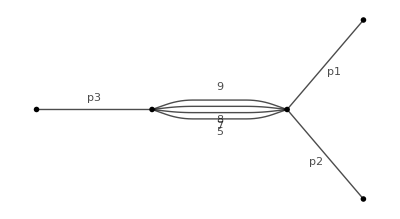
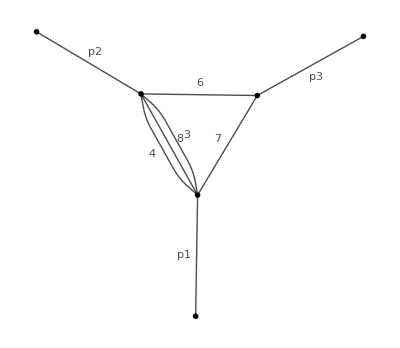
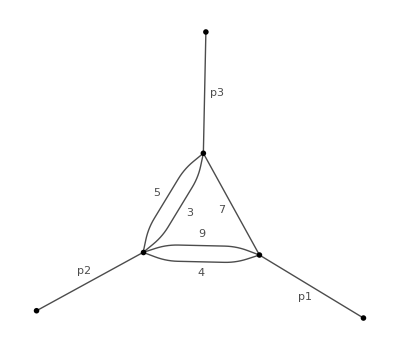
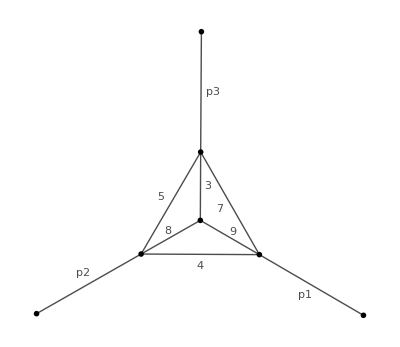
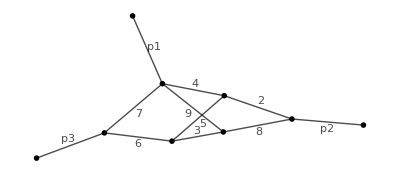
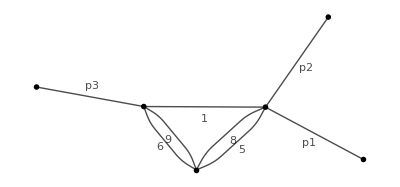
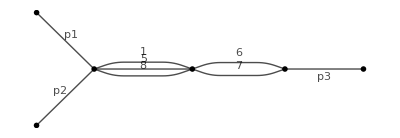
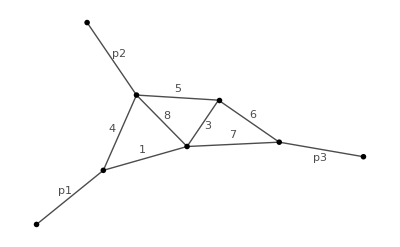

```mathematica
jGraphPlot/@todrawF6
```

#### F8

```mathematica
NewDsBasis[F8,{k1·k1,k2·k2,k3·k3,(-k1+p1)·(-k1+p1),(k1+p2)·(k1+p2),(-k1-k2+p1)·(-k1-k2+p1),(k1+k2-k3+p2)·(k1+k2-k3+p2),(k2-k3)·(k2-k3),(k1+k2+k3+p2)·(k1+k2+k3+p2),(k2+k3+p1)·(k2+k3+p1),(k1+k3)·(k1+k3),(k1+k2)·(k1+k2)},{k1,k2,k3},Directory->"F8dir"]
```

F8 is valid basis. The definitions of the basis will be saved in "F8dir" directory.
    Ds[F8] — denominators,
    SPs[F8] — scalar products involving loop momenta,
    LMs[F8] — loop momenta,
    EMs[F8] — external momenta,
    Parameters[F8] — parameters (invariants, masses, dimension),
    Toj[F8] — rules to transform scalar products to denominators,
    CutDs[F8] — flag vector of cut denominators.

F8

```mathematica
topo8={{1->2,0},{3->5,0},{5->6,0},{1->3,0},{2->4,0},{3->6,0},{4->6,0},{5->4,0},{-1->1,p1},{-2->2,p2},{-6->6, p3}}
```

{{1→2,0},{3→5,0},{5→6,0},{1→3,0},{2→4,0},{3→6,0},{4→6,0},{5→4,0},{-1→1,p1},{-2→2,p2},{-6→6,p3}}

```mathematica
AttachGraph[js[F8,1,1,1,1,1,1,1,1,1,0,0,0],topo8]
```

```mathematica
todrawF8=MastersF8/.{1,{a__}}:>j[F8,a]
```

{j[F8,0,0,1,0,1,1,0,1,0,0,0,0],j[F8,0,0,1,1,0,1,1,1,0,0,0,0],j[F8,0,0,1,1,1,1,1,0,0,0,0,0],j[F8,1,0,1,0,0,1,1,1,0,0,0,0],j[F8,1,1,1,0,0,1,1,1,0,0,0,0]}

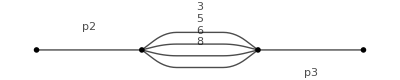
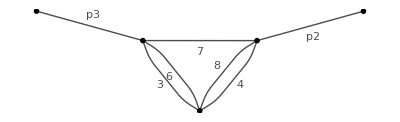
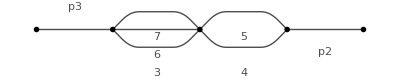
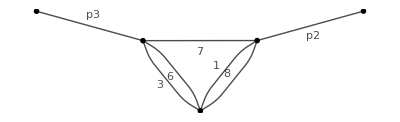
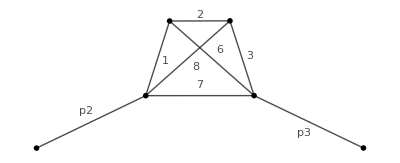

```mathematica
jGraphPlot/@todrawF8
```

#### F9

```mathematica
NewDsBasis[F9,{k1·k1,k2·k2,k3·k3,(-k1+p1)·(-k1+p1),(k1-k3+p2)·(k1-k3+p2),(-k1-k2+p1)·(-k1-k2+p1),(k1+k2-k3+p2)·(k1+k2-k3+p2),(k1-k3)·(k1-k3),(-k1-k2-k3+p1)·(-k1-k2-k3+p1),(k1+k2+k3+p2)·(k1+k2+k3+p2),(k1+k3+p2)·(k1+k3+p2),(k2+p2)·(k2+p2)},{k1,k2,k3},Directory->"F9dir"]
```

F9 is valid basis. The definitions of the basis will be saved in "F9dir" directory.
    Ds[F9] — denominators,
    SPs[F9] — scalar products involving loop momenta,
    LMs[F9] — loop momenta,
    EMs[F9] — external momenta,
    Parameters[F9] — parameters (invariants, masses, dimension),
    Toj[F9] — rules to transform scalar products to denominators,
    CutDs[F9] — flag vector of cut denominators.

F9

```mathematica
topo9={{1->5,0},{3->4,0},{5->6,0},{1->3,0},{2->4,0},{3->6,0},{4->6,0},{5->2,0},{-1->1,p1},{-2->2,p2},{-6->6,p3}}
```

{{1→5,0},{3→4,0},{5→6,0},{1→3,0},{2→4,0},{3→6,0},{4→6,0},{5→2,0},{-1→1,p1},{-2→2,p2},{-6→6,p3}}

```mathematica
AttachGraph[js[F9,1,1,1,1,1,1,1,1,1,0,0,0],topo9]
```

```mathematica
todrawF9=MastersF9/.{1,{a__}}:>j[F9,a]
```

{j[F9,0,0,1,1,0,1,1,1,0,0,0,0],j[F9,0,0,1,1,1,1,1,0,0,0,0,0],j[F9,0,1,1,0,1,1,0,0,0,0,0,0],j[F9,0,1,1,1,0,1,1,1,0,0,0,0],j[F9,1,0,1,1,1,1,1,1,0,0,0,0]}

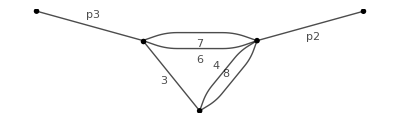
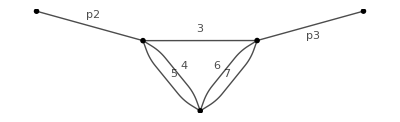
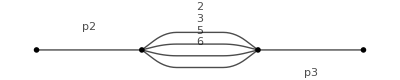
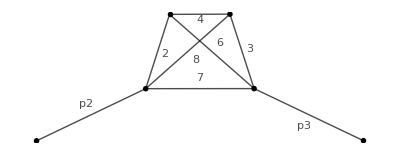
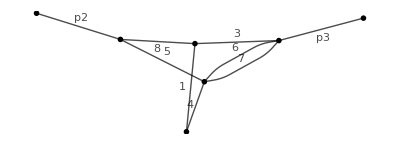

```mathematica
jGraphPlot/@todrawF9
```

#### Final results for all the integrals

```mathematica
FinalF1=ResF1/.{G[1,{a__}]:>j[F1,a]}/.Thread[todrawF1->jGraphPlot/@todrawF1]/.{d->4-2eps}
```

((-5+2 (4-2 eps)) (-8+3 (4-2 eps)) (704-400 (4-2 eps)+57 (4-2 eps)^2) (1-2 eps) -Graphics-)/(384 eps^5 r^5)+(7 (-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(48 eps^4 r^4)+(5 (-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(12 eps^4 r^4)+(7 (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(64 eps^4 r^4)-(7 (-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(24 eps^4 r^4)+(3 (-10+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(32 eps^3 r^3)+(3 (-10+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(32 eps^3 r^3)+((1-2 eps)^3 -Graphics-)/(8 eps^3 r^3)+-Graphics-/(2 r^2)

```mathematica
FinalF2=ResF2/.{G[1,{a__}]:>j[F2,a]}/.Thread[todrawF2->jGraphPlot/@todrawF2]/.{d->4-2eps}
```

-((-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (26396-11764 (4-2 eps)+1311 (4-2 eps)^2) (1-2 eps) -Graphics-)/(576 (-14+3 (4-2 eps)) (-22+5 (4-2 eps)) eps^5 r^4)+((-14+3 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(16 (-22+5 (4-2 eps)) eps^4 r^3)+(5 (-7+2 (4-2 eps)) (-14+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(24 (-22+5 (4-2 eps)) eps^4 r^3)-((-7+2 (4-2 eps)) (1220-580 (4-2 eps)+69 (4-2 eps)^2) (1-2 eps)^3 -Graphics-)/(18 (-14+3 (4-2 eps)) (-22+5 (4-2 eps)) eps^4 r^3)-((-7+2 (4-2 eps)) (-202+45 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(12 (-22+5 (4-2 eps)) eps^4 r^3)-(5 (-7+2 (4-2 eps)) (-18+5 (4-2 eps)) -Graphics-)/(36 eps^2 r^2)-(8 (-7+2 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(3 (-14+3 (4-2 eps)) (-22+5 (4-2 eps)) eps r^2)-((-7+2 (4-2 eps)) (-14+3 (4-2 eps)) (-10+3 (4-2 eps)) (1-2 eps) -Graphics-)/(4 (-22+5 (4-2 eps)) eps^3 r^2)-((-14+3 (4-2 eps)) -Graphics-)/((-22+5 (4-2 eps)) r)+((-14+3 (4-2 eps))^2 r -Graphics-)/(2 (-22+5 (4-2 eps)) eps)

```mathematica
FinalF3=ResF3/.{G[1,{a__}]:>j[F3,a]}/.Thread[todrawF3->jGraphPlot/@todrawF3]/.{d->4-2eps}
```

(5 (-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps) -Graphics-)/(64 eps^5 r^4)+((-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(3 eps^4 r^3)+((-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(3 eps^4 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(2 eps^4 r^3)-((-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(64 eps^4 r^3)+(3 (-7+2 (4-2 eps)) (-18+5 (4-2 eps)) -Graphics-)/(8 eps^2 r^2)+((-11+3 (4-2 eps)) -Graphics-)/(eps r)-((1-2 eps) -Graphics-)/(2 eps)

```mathematica
FinalF4=ResF4/.{G[1,{a__}]:>j[F4,a]}/.Thread[todrawF4->jGraphPlot/@todrawF4]/.{d->4-2eps}
```

-(5 (-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps) -Graphics-)/(96 eps^5 r^4)+((-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(3 eps^4 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(6 eps^4 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(6 eps^4 r^3)+(5 (1-2 eps) -Graphics-)/(2 eps r)+((-11+3 (4-2 eps)) -Graphics-)/(eps r)-((1-2 eps) -Graphics-)/(2 eps)

```mathematica
FinalF5=ResF5/.{G[1,{a__}]:>j[F5,a]}/.Thread[todrawF5->jGraphPlot/@todrawF5]/.{d->4-2eps}
```

-((-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (35982-16403 (4-2 eps)+1870 (4-2 eps)^2) (1-2 eps) -Graphics-)/(1152 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^5 r^4)+((-7+2 (4-2 eps)) (1306-579 (4-2 eps)+64 (4-2 eps)^2) (1-2 eps)^3 -Graphics-)/(24 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^4 r^3)+((-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(4 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^2 r^3)+((-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (10254-4645 (4-2 eps)+526 (4-2 eps)^2) (1-2 eps)^2 -Graphics-)/(48 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^4 r^3)+((-7+2 (4-2 eps)) (-57+13 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(36 (-9+2 (4-2 eps)) eps^4 r^3)+((-7+2 (4-2 eps)) (-18+5 (4-2 eps)) (14970-6773 (4-2 eps)+766 (4-2 eps)^2) -Graphics-)/(72 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^2 r^2)+(5 (-22+5 (4-2 eps)) (1-2 eps) -Graphics-)/(4 (-9+2 (4-2 eps)) eps r)-(5 (1-2 eps) -Graphics-)/(2 eps r)-((530-235 (4-2 eps)+26 (4-2 eps)^2) -Graphics-)/(2 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) r)+((-11+3 (4-2 eps)) (250-114 (4-2 eps)+13 (4-2 eps)^2) -Graphics-)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps r)+((-11+3 (4-2 eps)) (250-114 (4-2 eps)+13 (4-2 eps)^2) -Graphics-)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps r)-((-14+3 (4-2 eps)) (-13+3 (4-2 eps)) -Graphics-)/(2 (-22+5 (4-2 eps)) eps)-((-14+3 (4-2 eps)) r -Graphics-)/(-22+5 (4-2 eps))

```mathematica
FinalF6=ResF6/.{G[1,{a__}]:>j[F6,a]}/.Thread[todrawF6->jGraphPlot/@todrawF6]/.{d->4-2eps}
```

-((-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (-303+70 (4-2 eps)) (1-2 eps) -Graphics-)/(48 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^4 r^4)-((-7+2 (4-2 eps)) (-10+3 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(3 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^3 r^3)-((-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(2 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^2 r^3)+((-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (-84+19 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(3 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^3 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(3 (-9+2 (4-2 eps)) eps^3 r^3)+((-7+2 (4-2 eps)) (-18+5 (4-2 eps)) (-71+16 (4-2 eps)) -Graphics-)/(3 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps r^2)+(5 (1-2 eps) -Graphics-)/((-9+2 (4-2 eps)) r)-(16 eps^2 -Graphics-)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) r)+(4 (-13+3 (4-2 eps)) (-11+3 (4-2 eps)) -Graphics-)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) r)+(4 (-13+3 (4-2 eps)) (-11+3 (4-2 eps)) -Graphics-)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) r)-((-14+3 (4-2 eps)) -Graphics-)/(-22+5 (4-2 eps))+(2 (-14+3 (4-2 eps)) r -Graphics-)/(-22+5 (4-2 eps))

```mathematica
FinalF8=ResF8/.{G[1,{a__}]:>j[F8,a]}/.Thread[todrawF8->jGraphPlot/@todrawF8]/.{d->4-2eps}
```

((-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps) -Graphics-)/(18 eps^5 r^4)-((-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(18 eps^4 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(3 eps^4 r^3)-((-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 -Graphics-)/(64 eps^4 r^3)+(5 (-7+2 (4-2 eps)) (-18+5 (4-2 eps)) -Graphics-)/(72 eps^2 r^2)

```mathematica
FinalF9=ResF9/.{G[1,{a__}]:>j[F9,a]}/.Thread[todrawF9->jGraphPlot/@todrawF9]/.{d->4-2eps}
```

-(49 (-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps) -Graphics-)/(288 eps^5 r^4)+((-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(6 eps^4 r^3)-(17 (-7+2 (4-2 eps)) (1-2 eps)^3 -Graphics-)/(18 eps^4 r^3)+(5 (-7+2 (4-2 eps)) (-18+5 (4-2 eps)) -Graphics-)/(9 eps^2 r^2)+(5 (1-2 eps) -Graphics-)/(2 eps r)

#### Replacing in the master integral names

```mathematica
F1sub=((-5+2 (4-2 eps)) (-8+3 (4-2 eps)) (704-400 (4-2 eps)+57 (4-2 eps)^2) (1-2 eps) B41)/(384 eps^5 r^5)+(7 (-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 A51)/(48 eps^4 r^4)+(5 (-7+2 (4-2 eps)) (1-2 eps)^3 A52)/(12 eps^4 r^4)+(7 (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 B51)/(64 eps^4 r^4)-(7 (-7+2 (4-2 eps)) (1-2 eps)^3 B52)/(24 eps^4 r^4)+(3 (-10+3 (4-2 eps)) (1-2 eps)^2 B62)/(32 eps^3 r^3)+(3 (-10+3 (4-2 eps)) (1-2 eps)^2 C61)/(32 eps^3 r^3)+((1-2 eps)^3 B61)/(8 eps^3 r^3)+A73/(2 r^2);
```

```mathematica
F2sub=-((-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (26396-11764 (4-2 eps)+1311 (4-2 eps)^2) (1-2 eps) B41)/(576 (-14+3 (4-2 eps)) (-22+5 (4-2 eps)) eps^5 r^4)+((-14+3 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 B51)/(16 (-22+5 (4-2 eps)) eps^4 r^3)+(5 (-7+2 (4-2 eps)) (-14+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 A51)/(24 (-22+5 (4-2 eps)) eps^4 r^3)-((-7+2 (4-2 eps)) (1220-580 (4-2 eps)+69 (4-2 eps)^2) (1-2 eps)^3 A52)/(18 (-14+3 (4-2 eps)) (-22+5 (4-2 eps)) eps^4 r^3)-((-7+2 (4-2 eps)) (-202+45 (4-2 eps)) (1-2 eps)^3 B52)/(12 (-22+5 (4-2 eps)) eps^4 r^3)-(5 (-7+2 (4-2 eps)) (-18+5 (4-2 eps)) A62)/(36 eps^2 r^2)-(8 (-7+2 (4-2 eps)) (1-2 eps)^2 A61)/(3 (-14+3 (4-2 eps)) (-22+5 (4-2 eps)) eps r^2)-((-7+2 (4-2 eps)) (-14+3 (4-2 eps)) (-10+3 (4-2 eps)) (1-2 eps) A63)/(4 (-22+5 (4-2 eps)) eps^3 r^2)-((-14+3 (4-2 eps)) A73)/((-22+5 (4-2 eps)) r)+((-14+3 (4-2 eps))^2 r A91)/(2 (-22+5 (4-2 eps)) eps);
```

```mathematica
F3sub=(5 (-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps) B41)/(64 eps^5 r^4)+((-7+2 (4-2 eps)) (1-2 eps)^3 B52)/(3 eps^4 r^3)+((-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 A51)/(3 eps^4 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 A52)/(2 eps^4 r^3)-((-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 B51)/(64 eps^4 r^3)+(3 (-7+2 (4-2 eps)) (-18+5 (4-2 eps)) A62)/(8 eps^2 r^2)+((-11+3 (4-2 eps)) A75)/(eps r)-((1-2 eps) B81)/(2 eps);
```

```mathematica
F4sub=-(5 (-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps) B41)/(96 eps^5 r^4)+((-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 A51)/(3 eps^4 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 A52)/(6 eps^4 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 B52)/(6 eps^4 r^3)+(5 (1-2 eps) A71)/(2 eps r)+((-11+3 (4-2 eps)) A74)/(eps r)-((1-2 eps) C81)/(2 eps);
```

```mathematica
F5sub=-((-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (35982-16403 (4-2 eps)+1870 (4-2 eps)^2) (1-2 eps) B41)/(1152 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^5 r^4)+((-7+2 (4-2 eps)) (1306-579 (4-2 eps)+64 (4-2 eps)^2) (1-2 eps)^3 B52)/(24 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^4 r^3)+((-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 B51)/(4 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^2 r^3)+((-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (10254-4645 (4-2 eps)+526 (4-2 eps)^2) (1-2 eps)^2 A51)/(48 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^4 r^3)+((-7+2 (4-2 eps)) (-57+13 (4-2 eps)) (1-2 eps)^3 A52)/(36 (-9+2 (4-2 eps)) eps^4 r^3)+((-7+2 (4-2 eps)) (-18+5 (4-2 eps)) (14970-6773 (4-2 eps)+766 (4-2 eps)^2) A62)/(72 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^2 r^2)+(5 (-22+5 (4-2 eps)) (1-2 eps) A71)/(4 (-9+2 (4-2 eps)) eps r)-(5 (1-2 eps) A72)/(2 eps r)-((530-235 (4-2 eps)+26 (4-2 eps)^2) A73)/(2 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) r)+((-11+3 (4-2 eps)) (250-114 (4-2 eps)+13 (4-2 eps)^2) A74)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps r)+((-11+3 (4-2 eps)) (250-114 (4-2 eps)+13 (4-2 eps)^2) A75)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps r)-((-14+3 (4-2 eps)) (-13+3 (4-2 eps)) A81)/(2 (-22+5 (4-2 eps)) eps)-((-14+3 (4-2 eps)) r A92)/(-22+5 (4-2 eps));
```

```mathematica
F6sub=-((-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (-303+70 (4-2 eps)) (1-2 eps) B41)/(48 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^4 r^4)-((-7+2 (4-2 eps)) (-10+3 (4-2 eps)) (1-2 eps)^3 B52)/(3 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^3 r^3)-((-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 B51)/(2 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^2 r^3)+((-7+2 (4-2 eps)) (-8+3 (4-2 eps)) (-84+19 (4-2 eps)) (1-2 eps)^2 A51)/(3 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps^3 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 A52)/(3 (-9+2 (4-2 eps)) eps^3 r^3)+((-7+2 (4-2 eps)) (-18+5 (4-2 eps)) (-71+16 (4-2 eps)) A62)/(3 (-9+2 (4-2 eps)) (-22+5 (4-2 eps)) eps r^2)+(5 (1-2 eps) A71)/((-9+2 (4-2 eps)) r)-(16 eps^2 A73)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) r)+(4 (-13+3 (4-2 eps)) (-11+3 (4-2 eps)) A74)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) r)+(4 (-13+3 (4-2 eps)) (-11+3 (4-2 eps)) A75)/((-9+2 (4-2 eps)) (-22+5 (4-2 eps)) r)-((-14+3 (4-2 eps)) A81)/(-22+5 (4-2 eps))+(2 (-14+3 (4-2 eps)) r A92)/(-22+5 (4-2 eps));
```

```mathematica
F8sub=((-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps) B41)/(18 eps^5 r^4)-((-7+2 (4-2 eps)) (1-2 eps)^3 B52)/(18 eps^4 r^3)+((-7+2 (4-2 eps)) (1-2 eps)^3 A52)/(3 eps^4 r^3)-((-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2 B51)/(64 eps^4 r^3)+(5 (-7+2 (4-2 eps)) (-18+5 (4-2 eps)) A62)/(72 eps^2 r^2);
```

```mathematica
F9sub=-(49 (-7+2 (4-2 eps)) (-5+2 (4-2 eps)) (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps) B41)/(288 eps^5 r^4)+((-7+2 (4-2 eps)) (1-2 eps)^3 B51)/(6 eps^4 r^3)-(17 (-7+2 (4-2 eps)) (1-2 eps)^3 A52)/(18 eps^4 r^3)+(5 (-7+2 (4-2 eps)) (-18+5 (4-2 eps)) A61)/(9 eps^2 r^2)+(5 (1-2 eps) A71)/(2 eps r);
```